#### Метод Рунге - Кутты для решения задачи Коши для однородного дифференциального уравнения 1 - го порядка

Analytics

```mathematica
ys[t_] = DSolve[{y'[t]==-2y[t]-t^2,y[0]==1},y[t],t][[1,1,2]]
zs[t_]=DSolve[{z'[t]==-z[t]-2t,z[0.5]==ys[0.5]},z[t],t][[1,1,2]]
αs=zs[0]
```

-1/4 ⅇ^(-2 t) (-5+ⅇ^(2 t)-2 ⅇ^(2 t) t+2 ⅇ^(2 t) t^2)

-2. ⅇ^-t (0.548324-1. ⅇ^t+ⅇ^t t)

0.903352

Euler Method

```mathematica
a = -2;
y'[x_,y_]:= a * y - x^2;
Subscript[y, 0]=1;
Subscript[x, 0]=0;
z'[x_,z_]:=-z+a*x;
h=0.1;
```

```mathematica
Do[Subscript[x, i]=Subscript[x, i-1]+h,{i,1,5}];
Do[Subscript[y, i]=Subscript[y, i-1]+h*y'[Subscript[x, i-1],Subscript[y, i-1]],{i,1,5}];
Subscript[y, 5]
Subscript[z, 5]=Subscript[y, 5];
Do[Subscript[z, i]=Subscript[z, i+1]-h*z'[Subscript[x, i+1],Subscript[z, i+1]],{i,0,4}];
Subscript[z, 0]
```

0.301408

1.22245

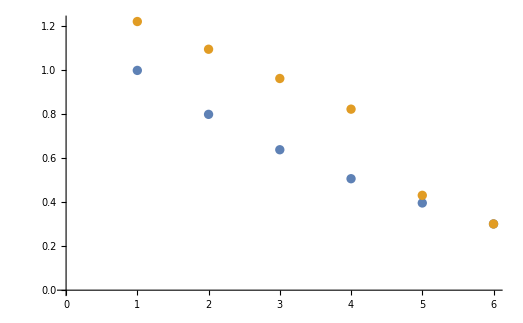

1.22245

```mathematica
ListPlot[{Table[Subscript[y, i],{i,0,5}],Table[Subscript[z, i],{i,0,5}]}]
Print[Subscript[z, 0]]
```

Euler Cachy Method

```mathematica
Do[Unset[Subscript[y, i]],{i,0,5}]
Do[Unset[Subscript[z, i]],{i,0,5}]
a = -2;
y'[x_,y_]:= a * y - x^2;
Subscript[y, 0]=1;
Subscript[x, 0]=0;
z'[x_,z_]:=-z+a*x;
h=0.1;
```

```mathematica
For[i=1,i≤5,i++,
Subscript[ỹ, i]=Subscript[y, i-1]+h*y'[Subscript[x, i-1],Subscript[y, i-1]];
Subscript[y, i]=Subscript[y, i-1]+0.5*h(y'[Subscript[x, i-1],Subscript[y, i-1]] + y'[Subscript[x, i],Subscript[ỹ, i]]);
Print[Subscript[y, i]];
];
```

0.8195

0.66959

0.542964

0.43363

0.336677

```mathematica
Subscript[z, 5]=Subscript[y, 5]
For[i=4,i≥0,i--,
Subscript[z̃, i]=Subscript[z, i+1]-h*z'[Subscript[x, i+1],Subscript[z, i+1]];
Subscript[z, i]=Subscript[z, i+1]-0.5*h(z'[Subscript[x, i+1],Subscript[z, i+1]] + z'[Subscript[x, i],Subscript[z̃, i]]);
Print[Subscript[z, i]];
];
```

0.50177

0.649456

0.791649

0.927772

1.05719

1.17919

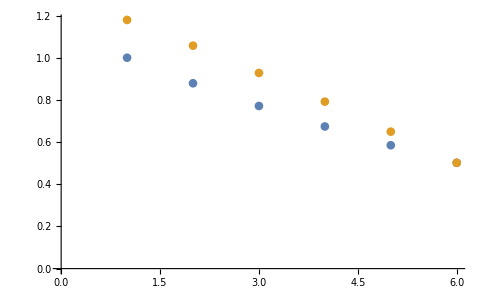

1.17919

```mathematica
ListPlot[{Table[Subscript[y, i],{i,0,5}],Table[Subscript[z, i],{i,0,5}]}]
Print[Subscript[z, 0]]
```

Traditional Runge Kutta Method

```mathematica
Do[Unset[Subscript[y, i]],{i,0,5}]
Do[Unset[Subscript[z, i]],{i,0,5}]
a = -2;
y'[x_,y_]:= a * y - x^2;
Subscript[y, 0]=1;
Subscript[x, 0]=0;
z'[x_,z_]:=-z+a*x;
h=0.1;
koeff=1/6;
```

```mathematica
For[i=1,i≤5,i++,
Subscript[k, 1]=h*y'[Subscript[x, i-1],Subscript[y, i-1]];
Subscript[k, 2]=h*y'[Subscript[x, i-1]+0.5*h,Subscript[y, i-1]+0.5*Subscript[k, 1]];
Subscript[k, 3]=h*y'[Subscript[x, i-1]+0.5*h,Subscript[y, i-1]+0.5*Subscript[k, 2]];
Subscript[k, 4]=h*y'[Subscript[x, i-1]+h,Subscript[y, i-1]+Subscript[k, 3]];
Subscript[y, i]=Subscript[y, i-1]+koeff*(Subscript[k, 1]+2 Subscript[k, 2]+2 Subscript[k, 3]+Subscript[k, 4]);
Print[Subscript[y, i]]
];
```

0.818416

0.667904

0.541019

0.431666

0.334854

```mathematica
Subscript[z, 5]=Subscript[y, 5]
For[i=4,i≥0,i--,
Subscript[k, 1]=-h*z'[Subscript[x, i+1],Subscript[z, i+1]];
Subscript[k, 2]=-h*z'[Subscript[x, i+1]+0.5*h,Subscript[z, i+1]+0.5*Subscript[k, 1]];
Subscript[k, 3]=-h*z'[Subscript[x, i+1]+0.5*h,Subscript[z, i+1]+0.5*Subscript[k, 2]];
Subscript[k, 4]=-h*z'[Subscript[x, i+1]+h,Subscript[z, i+1]+Subscript[k, 3]];
Subscript[z, i]=Subscript[z, i+1]+koeff*(Subscript[k, 1]+2 Subscript[k, 2]+2 Subscript[k, 3]+Subscript[k, 4]);
Print[Subscript[z, i]];
];
```

0.334854

0.485583

0.63113

0.770951

0.904443

1.03094

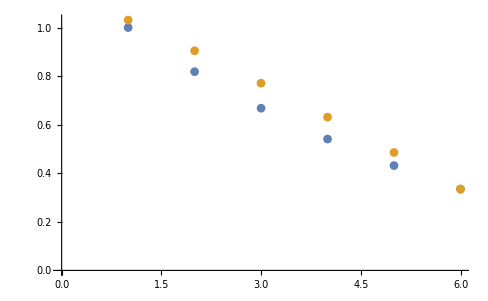

1.03094

```mathematica
ListPlot[{Table[Subscript[y, i],{i,0,5}],Table[Subscript[z, i],{i,0,5}]}]
Print[Subscript[z, 0]];
```